```mathematica
SetOptions[InputNotebook[],AutoGeneratedPackage->None]
```

```mathematica
(* get the radius function right *)
```

## Styles and files

```mathematica
runsToGenerate  = {};
```

```mathematica
(* PersistentSymbol["persistentGitHubPackage","Local"]="C:\\Users\\jonat\\Documents\\GitHub\\GeometricalPhyllotaxis"
*)

githubMathematica = PersistentSymbol["persistentGitHubMathematica"];
AppendTo[$Path,FileNameJoin[{githubMathematica,"Packages"}]];
githubRepo = PersistentSymbol["persistentGitHubRepo"];
Needs["LatticePhyllotaxis`"];
Needs["DiskStacking`"];
Get["scpPaperStylings.m"]

Needs["Wolfram`GitLink`"];
gitProperties [repo_]:= Module[{r,h,c},
r=GitOpen[repo];
h = r["HeadBranch"];
c=ToGitObject[r,h];
KeyTake[GitProperties[c],{"Author","SHA"}]
];
gitRepoProperties = gitProperties[githubRepo];
```

```mathematica
gDrive = PersistentSymbol["persistentGDrive"];
runDirectory = FileNameJoin[{gDrive,"Work\\Textbook\\Runs"}];
draftFigureDirectory = FileNameJoin[{gDrive,"Work\\Image bank\\Phyllobank\\Mathematica"}];

getRunByTag[tag_] := Module[{file,res},
file = FileNameJoin[{runDirectory,StringJoin[tag,".mx"]}];
If[!FileExistsQ[file],Print["Can't load ", tag, " from nonexistent", file];Abort[]];
res = Import[file];
If[!KeyMemberQ[res,"Run"],Print["Can't find Run in ", tag, " from ", file];Abort[]];
res["Run"]
];
```

```mathematica
jParastichyColour[n_] := jStyle["ParastichyColour"][n];
jFont[n_] := {FontFamily->  jStyle["FontFamily"],FontSize-> n};
paraColours= <|Red-> jParastichyColour[1],Blue-> jParastichyColour[2]|>;
leftRightColours = <|"Left"-> jParastichyColour[1],"Right"-> jParastichyColour[2]|>;
jBaseStyle= jFont[12];

SetAttributes[jExport,HoldFirst];

jExport[fig_] := Module[{figname},
SetDirectory[draftFigureDirectory];
figname=SymbolName[Unevaluated[fig]];
Export[StringJoin[figname,".jpg"],fig,ImageResolution->300];Export[StringJoin[figname,".pdf"],fig,ImageResolution->300];
ResetDirectory[];
fig
];
```

## tlkNonOpposed Illustrative lattice plot

```mathematica
tlkShowParastichyLines[lattice_,lineColourFunction_]  :=  Module[{ll,llines,paraset,plines,numbers,rise,divergence,glines},
ll =Take[Flatten[ LatticePhyllotaxis`latticeLabel[lattice]],2];
llines = Map[LatticePhyllotaxis`latticeParastichyLines[lattice,#]&,ll];
numbers= KeyValueMap[Style[Text[#1,#2],Background->White]&,KeyTake[lattice["namedLatticePoints"],Range[0,10]]];
rise= Translate[Arrow[{{lattice["namedLatticePoints"][1][[1]],lattice["namedLatticePoints"][0][[2]]},lattice["namedLatticePoints"][1]}],{0.05,0}];
divergence= {Arrow[{lattice["namedLatticePoints"][0],{lattice["namedLatticePoints"][1][[1]],lattice["namedLatticePoints"][0][[2]]}}]};
Graphics[{
{jStyle["CylinderColour"],LatticePhyllotaxis`latticeGraphicsCylinder[lattice]}
,{FaceForm[White],LatticePhyllotaxis`latticeCircles[lattice]/. Circle->Disk},
, {Thick,MapIndexed[{lineColourFunction[First[#2]],#1}&,llines]}
,{PointSize[Small],Point[LatticePhyllotaxis`latticePoints[lattice]]}
},PlotRange->{{-1/2,.6},{-0.05,0.4}}
,BaseStyle->Directive[FontFamily-> jStyle["FontFamily"],FontSize->Scaled[0.03]]
]
];

tlkNonOpposed := Module[{lattice,dh},
dh=LatticePhyllotaxis`latticeDivergenceRiseForNonOpposedTC[{2,5}];
lattice = LatticePhyllotaxis`latticeFromDivergenceRise[dh, {-0.1,0.5}];

tlkShowParastichyLines[lattice,jParastichyColour]
];
tlkOpposed := Module[{lattice,dh},
dh=LatticePhyllotaxis`latticeDivergenceRiseForOpposedTC[{2,5}];
lattice = LatticePhyllotaxis`latticeFromDivergenceRise[dh, {-0.1,0.5}];

tlkShowParastichyLines[lattice,jParastichyColour]
];
tlkONotO := GraphicsRow[{tlkOpposed,tlkNonOpposed}]
```

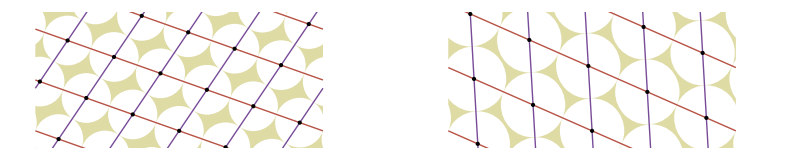

```mathematica
jExport[tlkONotO]
```

## Multirun code

```mathematica
doOneRun[parameters_] := Module[{run},
run = DiskStacking`runFromLattice[parameters["Lattice"]];
run= readyRunFromParameter[run,parameters] ; 
run=doMonitoredRun[run];
saveRunByTag[run];
run
];
retrieveRFunction[savedRun_] := Module[{run,parameters},
parameters=savedRun["Arena"];
run = DiskStacking`runFromLattice[parameters["Lattice"]];
run= readyRunFromParameter[run,parameters] ; 
run["Arena"]["rFunction"]
];

restartOneRun[lastRun_] := Module[{run},
run=lastRun;
run = DiskStacking`restartRunFromRun[run];
run= readyRunFromParameter[run,lastRun["Arena"]] ; 
run=doMonitoredRun[run];
saveRunByTag[run];
run
]

doMonitoredRun[run_] := Module[{res},
SeedRandom[run["Arena"]["Run"]];
res=run;
monitorRun= res["Arena"]["Run"];
monitorPP = <|"Noise"->res["Arena"]["Noise"],"rSlope"->res["Arena"]["rSlope"]|>;
res = DiskStacking`executeRun[res]; 
res 
];


saveRunByTag[run_] :=  Module[{parameters,saveFile,saveRun,tag},
parameters=run["Arena"];
tag=parameters["Tag"];
If[MissingQ[tag],tag="runData"];
saveFile= FileNameJoin[ {runDirectory,tag <> ToString[parameters["Run"]] <> ".mx"}];
saveRun =<|"File"->saveFile,"Run"->run|>;
Export[saveFile,saveRun];
run
];


doRunSets[parameterSets_] := Module[{res,abortCheck,runSets,timing},
abortCheck[parameterSet_] := CheckAbort[doOneRun[parameterSet],Print["Abort running ",parameterSet["Run"]]; Missing[parameterSet["Run"]]];
monitorRunTotal = Length[parameterSets];
monitorRunNumber= 0;
{timing,res}= Timing[Monitor[runSets=Map[(monitorRunNumber++;abortCheck[#]&),parameterSets],{monitorRunTotal,monitorRunNumber,monitorRun,monitorPP}];];
runSets
];


runExtractNonOverlappingChains[file_] := Module[{res},
monitorFile=file;
res=Import[file]["Run"];
DiskStacking`postRunExtractNonOverlappingChains[res]
];
```

```mathematica
latestRadius[run_] := Last@Values[DiskStacking`runDisksRadius[run]];
latestCentre[run_] := Last@Values[DiskStacking`runDisksHeight[run]];

readyRunFromParameter[lastRun_,experimentParameters_] := Module[{runParameters,run,arena},

(* set defaults *)
runParameters= <|
"Lattice"->LatticePhyllotaxis`latticeOrthogonal[{0,1}],
"zMax"->Missing[],
"runNumber"->1,
"diskMax"->∞,
"PostFixChains"->0,
"Run"->"",
"Noise"->Missing[]
|>;

runParameters= Append[runParameters,experimentParameters];
run=lastRun;


run["Arena"] = createRFunctionArena[{latestCentre[run],latestRadius[run]},runParameters];
run["Arena"]["GitHub"] = gitRepoProperties;
run
];


createRFunctionArena[{initialZ_ ,initialRadius_},runParameters_] := Module[{calcfunctionParameters,inverseLinearDecreaseFunctionParameters,linearFunctionParameters,constFunctionParameters,
arena,sectionStartRadius,sectionStartZ,functionCount,rFunctionPieces,lookup,z},

calcfunctionParameters[functionParameter_] := Switch[functionParameter["Type"],
"Constant",constFunctionParameters[functionParameter]
,
"LinearReduction",linearFunctionParameters[functionParameter]
,
"LinearCircumferenceIncrease",inverseLinearDecreaseFunctionParameters[functionParameter]
,
_,
 Print["Type not set ",functionParameter];Abort[];
];
inverseLinearDecreaseFunctionParameters[functionParameter_] := Module[{res,circumferenceStart,circumferenceScale,rStart,circumferenceEnd,rEnd,zEnd,func},
circumferenceStart = 1/sectionStartRadius;
circumferenceEnd = circumferenceStart* functionParameter["circumferenceScale"];
zEnd = sectionStartZ+functionParameter["zRange"];
res = Append[functionParameter,
<|"rStart"-> sectionStartRadius
,"rEnd"->  sectionStartRadius/functionParameter["circumferenceScale"]
,"rScale"-> 1/functionParameter["circumferenceScale"]
,"zStart"-> sectionStartZ
,"zEnd"-> zEnd|>
];
func = Function[{z},sectionStartRadius*(zEnd-sectionStartZ) / (-(z-zEnd) +(functionParameter["circumferenceScale"])*( z-sectionStartZ))];
res["rFunction"] = functionClosure[func];

sectionStartZ = res["zEnd"];
sectionStartRadius = res["rEnd"];
res
];
linearFunctionParameters[functionParameter_] := Module[{res,rStart,rEnd},
res = Append[functionParameter,
<|"rStart"-> sectionStartRadius,
"rEnd"-> sectionStartRadius/functionParameter["rScale"]
,"zStart"-> sectionStartZ|>
];
res = Append[res,linearFunctionProperties[ {res["rStart"],res["rEnd"]},res["rSlope"],sectionStartZ]];

sectionStartZ = res["zEnd"];
sectionStartRadius = res["rEnd"];
res
];
constFunctionParameters[functionParameter_] := Module[{res,finalRadius},
res = Append[functionParameter,
<|"rStart"-> sectionStartRadius
,"rEnd"-> sectionStartRadius
,"zStart"-> sectionStartZ
,"zEnd"-> sectionStartZ + functionParameter["ApproximateChains"]* 4* sectionStartRadius
|>];
res = Append[res,<|"rFunction"->Function[{z},Evaluate[sectionStartRadius]]|>];
sectionStartZ = res["zEnd"];
res
];
(*
functionListToPieceWise[flist_] := Module[{piece,pieceFunction},
piece [z_] := KeyValueMap[{(lookup[#1]),#2["zStart"]<z< #2["zEnd"]}&,flist];
pieceFunction[z_] := Evaluate[Piecewise[piece[zq]] /. zq->z];
pieceFunction
];
*)

sectionStartZ =  initialZ;
sectionStartRadius = initialRadius;
functionCount = 1;

arena = runParameters;
arena["rFunctionList"] = Association@Map[functionCount++->calcfunctionParameters[#]&,arena["radiusFunctionParameters"]];

bq=KeyValueMap[{(lookup[#1]),#2["zStart"]<z<= #2["zEnd"]}&,arena["rFunctionList"]];
bq = Prepend[bq,{arena["rFunctionList"][1]["rStart"],z<= arena["rFunctionList"][1]["zStart"]}];
bq = Append[bq,{Last[arena["rFunctionList"]]["rEnd"],z > (Last[arena["rFunctionList"]])["zEnd"]}];

rFunctionPieces = bq  /. lookup[i_] :> arena["rFunctionList"][i]["rFunction"][z];

arena["rFunctionPieces"] = rFunctionPieces ;
arena["rFunction"] := Function[{zq},Piecewise[arena["rFunctionPieces"]]/. z-> zq]; 
arena["zMax"] = (Last[arena["rFunctionList"]])["zEnd"]; 
arena

];


linearFunctionProperties[ {rStart_,rEnd_},rSlope_,zStart_,power_:1] := Module[{zSlopeRange,zEnd,func,rDash,scaler},
rDash = -rSlope;
scaler = Sign[rDash]*(Abs[(zEnd-zStart) * rDash] )^ (power-1);
zEnd = zStart + ( (rEnd-rStart))/rDash ;

func = Function[{z},rStart+(((z-zStart) * Abs[rDash])^power)/scaler];
func  = functionClosure[func];
<|"rFunction"-> func, "zEnd"-> zEnd|>
]


functionClosure[f_] := Function[{z$},Evaluate[f[[2]]]]
```

## based on scpConeTransformation

### Get run

```mathematica
arena2= <|"runNumber"->1
,"Tag"->"tlk-radius-34bis-crecrease"
,"Run"->""
,"diskMax"-> 177
,"radiusFunctionParameters" -> {
<|"Type"->"LinearCircumferenceIncrease","circumferenceScale"->1.7,
"zRange"-> 0.1|>
,<|"Type"->"Constant","ApproximateChains"->1|>
,<|"Type"->"LinearCircumferenceIncrease","circumferenceScale"-> 0.9,"zRange"->0.02|>
,<|"Type"->"LinearCircumferenceIncrease","circumferenceScale"-> 0.4/0.9,"zRange"->0.15|>
,<|"Type"->"LinearCircumferenceIncrease","circumferenceScale"-> 0.2/(0.4/0.9),"zRange"->0.15|>
}
,"Noise"->0
,"Lattice"->LatticePhyllotaxis`latticeOrthogonal[{21,34},cylinderLU={-0.01,0.1}]
|>;
(*
runCone2  = doOneRun[arena2];

*)
```

```mathematica
runCone = getRunByTag["tlk-radius-34bis-crecrease"];
runCone["Arena"]
```

<|rScale→10,rSlope→0.03,power→1,zMax→0.549001,diskMax→∞,PostFixChains→0,runNumber→1,Tag→tlk-radius-34bis-crecrease,Run→,radiusFunctionParameters→{<|Type→LinearCircumferenceIncrease,circumferenceScale→1.7,zRange→0.1|>,<|Type→Constant,ApproximateChains→1|>,<|Type→LinearCircumferenceIncrease,circumferenceScale→0.9,zRange→0.02|>,<|Type→LinearCircumferenceIncrease,circumferenceScale→0.444444,zRange→0.15|>,<|Type→LinearCircumferenceIncrease,circumferenceScale→0.45,zRange→0.15|>},Noise→0,Lattice→<|parastichyNumbers→<|{21,34}→1/1597,{55}→2/1597|>,d→610/1597,h→1/1597,Jugacy→1,cylinder→{{-1/2,1/2},{-0.01,0.1}},nodeCylinder→{{-1/2,1/2},{-0.01,0.1}},parastichyVectors→<|34→{-21/1597,34/1597},21→{34/1597,21/1597},55→{13/1597,55/1597}|>,scalings→<||>,namedLatticePoints→<|-15→{0.270507,-0.00939261},-14→{-0.347527,-0.00876644},-13→{0.0344396,-0.00814026},-12→{0.416406,-0.00751409},-11→{-0.201628,-0.00688791},-10→{0.180338,-0.00626174},-9→{-0.437696,-0.00563557},-8→{-0.0557295,-0.00500939},-7→{0.326237,-0.00438322},-6→{-0.291797,-0.00375704},-5→{0.0901691,-0.00313087},-4→{0.472135,-0.0025047},-3→{-0.145899,-0.00187852},-2→{0.236068,-0.00125235},-1→{-0.381966,-0.000626174},0→{0.,0.},1→{0.381966,0.000626174},2→{-0.236068,0.00125235},3→{0.145899,0.00187852},4→{-0.472135,0.0025047},5→{-0.0901691,0.00313087},6→{0.291797,0.00375704},7→{-0.326237,0.00438322},8→{0.0557295,0.00500939},9→{0.437696,0.00563557},10→{-0.180338,0.00626174},11→{0.201628,0.00688791},12→{-0.416406,0.00751409},13→{-0.0344396,0.00814026},14→{0.347527,0.00876644},15→{-0.270507,0.00939261},16→{0.111459,0.0100188},17→{0.493425,0.010645},18→{-0.124609,0.0112711},19→{0.257358,0.0118973},20→{-0.360676,0.0125235},21→{0.0212899,0.0131497},22→{0.403256,0.0137758},23→{-0.214778,0.014402},24→{0.167188,0.0150282},25→{-0.450845,0.0156544},26→{-0.0688791,0.0162805},27→{0.313087,0.0169067},28→{-0.304947,0.0175329},29→{0.0770194,0.018159},30→{0.458986,0.0187852},31→{-0.159048,0.0194114},32→{0.222918,0.0200376},33→{-0.395116,0.0206637},34→{-0.0131497,0.0212899},35→{0.368817,0.0219161},36→{-0.249217,0.0225423},37→{0.132749,0.0231684},38→{-0.485285,0.0237946},39→{-0.103319,0.0244208},40→{0.278647,0.025047},41→{-0.339386,0.0256731},42→{0.0425798,0.0262993},43→{0.424546,0.0269255},44→{-0.193488,0.0275517},45→{0.188478,0.0281778},46→{-0.429555,0.028804},47→{-0.0475892,0.0294302},48→{0.334377,0.0300564},49→{-0.283657,0.0306825},50→{0.0983093,0.0313087},51→{0.480276,0.0319349},52→{-0.137758,0.0325611},53→{0.244208,0.0331872},54→{-0.373826,0.0338134},55→{0.00814026,0.0344396},56→{0.390106,0.0350657},57→{-0.227927,0.0356919},58→{0.154039,0.0363181},59→{-0.463995,0.0369443},60→{-0.0820288,0.0375704},61→{0.299937,0.0381966},62→{-0.318096,0.0388228},63→{0.0638698,0.039449},64→{0.445836,0.0400751},65→{-0.172198,0.0407013},66→{0.209768,0.0413275},67→{-0.408265,0.0419537},68→{-0.0262993,0.0425798},69→{0.355667,0.043206},70→{-0.262367,0.0438322},71→{0.119599,0.0444584},72→{-0.498435,0.0450845},73→{-0.116468,0.0457107},74→{0.265498,0.0463369},75→{-0.352536,0.0469631},76→{0.0294302,0.0475892},77→{0.411396,0.0482154},78→{-0.206637,0.0488416},79→{0.175329,0.0494678},80→{-0.442705,0.0500939},81→{-0.0607389,0.0507201},82→{0.321227,0.0513463},83→{-0.296807,0.0519724},84→{0.0851597,0.0525986},85→{0.467126,0.0532248},86→{-0.150908,0.053851},87→{0.231058,0.0544771},88→{-0.386976,0.0551033},89→{-0.00500939,0.0557295},90→{0.376957,0.0563557},91→{-0.241077,0.0569818},92→{0.140889,0.057608},93→{-0.477145,0.0582342},94→{-0.0951785,0.0588604},95→{0.286788,0.0594865},96→{-0.331246,0.0601127},97→{0.0507201,0.0607389},98→{0.432686,0.0613651},99→{-0.185348,0.0619912},100→{0.196619,0.0626174},101→{-0.421415,0.0632436},102→{-0.039449,0.0638698},103→{0.342517,0.0644959},104→{-0.275517,0.0651221},105→{0.10645,0.0657483},106→{0.488416,0.0663745},107→{-0.129618,0.0670006},108→{0.252348,0.0676268},109→{-0.365686,0.068253},110→{0.0162805,0.0688791},111→{0.398247,0.0695053},112→{-0.219787,0.0701315},113→{0.162179,0.0707577},114→{-0.455855,0.0713838},115→{-0.0738885,0.07201},116→{0.308078,0.0726362},117→{-0.309956,0.0732624},118→{0.07201,0.0738885},119→{0.453976,0.0745147},120→{-0.164058,0.0751409},121→{0.217909,0.0757671},122→{-0.400125,0.0763932},123→{-0.018159,0.0770194},124→{0.363807,0.0776456},125→{-0.254227,0.0782718},126→{0.12774,0.0788979},127→{-0.490294,0.0795241},128→{-0.108328,0.0801503},129→{0.273638,0.0807765},130→{-0.344396,0.0814026},131→{0.0375704,0.0820288},132→{0.419537,0.082655},133→{-0.198497,0.0832812},134→{0.183469,0.0839073},135→{-0.434565,0.0845335},136→{-0.0525986,0.0851597},137→{0.329368,0.0857858},138→{-0.288666,0.086412},139→{0.0932999,0.0870382},140→{0.475266,0.0876644},141→{-0.142768,0.0882905},142→{0.239198,0.0889167},143→{-0.378835,0.0895429},144→{0.00313087,0.0901691},145→{0.385097,0.0907952},146→{-0.232937,0.0914214},147→{0.149029,0.0920476},148→{-0.469004,0.0926738},149→{-0.0870382,0.0932999},150→{0.294928,0.0939261},151→{-0.323106,0.0945523},152→{0.0588604,0.0951785},153→{0.440827,0.0958046},154→{-0.177207,0.0964308},155→{0.204759,0.097057},156→{-0.413275,0.0976832},157→{-0.0313087,0.0983093},158→{0.350657,0.0989355},159→{-0.267376,0.0995617}|>|>,rFunctionList→<|1→<|Type→LinearCircumferenceIncrease,circumferenceScale→1.7,zRange→0.1,rStart→0.0125117,rEnd→0.00735984,rScale→0.588235,zStart→0.0995617,zEnd→0.199562,rFunction→Function[{z$},0.00125117/(0.199562+1.7 (-0.0995617+z$)-z$)]|>,2→<|Type→Constant,ApproximateChains→1,rStart→0.00735984,rEnd→0.00735984,zStart→0.199562,zEnd→0.229001,rFunction→Function[{z$},0.00735984]|>,3→<|Type→LinearCircumferenceIncrease,circumferenceScale→0.9,zRange→0.02,rStart→0.00735984,rEnd→0.0081776,rScale→1.11111,zStart→0.229001,zEnd→0.249001,rFunction→Function[{z$},0.000147197/(0.249001+0.9 (-0.229001+z$)-z$)]|>,4→<|Type→LinearCircumferenceIncrease,circumferenceScale→0.444444,zRange→0.15,rStart→0.0081776,rEnd→0.0183996,rScale→2.25,zStart→0.249001,zEnd→0.399001,rFunction→Function[{z$},0.00122664/(0.399001+0.444444 (-0.249001+z$)-z$)]|>,5→<|Type→LinearCircumferenceIncrease,circumferenceScale→0.45,zRange→0.15,rStart→0.0183996,rEnd→0.040888,rScale→2.22222,zStart→0.399001,zEnd→0.549001,rFunction→Function[{z$},0.00275994/(0.549001+0.45 (-0.399001+z$)-z$)]|>|>,rFunctionPieces→{{0.0125117,z≤0.0995617},{0.00125117/(0.199562+1.7 (-0.0995617+z)-z),0.0995617<z≤0.199562},{0.00735984,0.199562<z≤0.229001},{0.000147197/(0.249001+0.9 (-0.229001+z)-z),0.229001<z≤0.249001},{0.00122664/(0.399001+0.444444 (-0.249001+z)-z),0.249001<z≤0.399001},{0.00275994/(0.549001+0.45 (-0.399001+z)-z),0.399001<z≤0.549001},{0.040888,z>0.549001}},rFunction:>Function[{zq$},Piecewise[arena$26393[rFunctionPieces]]/.z→zq$]|>

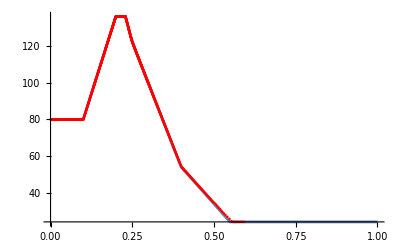

```mathematica
getf= retrieveRFunction[runCone] ; ht=runDisksHeight[runCone]; ra=runDisksRadius[runCone]; getr = Map[{ht[#],1/ra[#]}&,
Select[diskNumbersInRun[runCone],#>0&]];
Show[{Plot[1/getf[z],{z,0,1}],
ListPlot[getr,PlotStyle->Red]}]
```

### Disk map

```mathematica
diskTransform[{zMin_,zMax_}] := Module[{f},
f= Function[{xz},Module[{x,z,r},
{x,z}=xz;
r = zMax- z;
r= r/(zMax-zMin); (* outer ring radius 1 *)
r*{Cos[2 π x],Sin [ 2 π x]} 
]
];
f
];
```

```mathematica
makeDiskGraphics[run_] :=Module[{(*runDiskTransform,namedPolygons,namedType,namedPoints,colouredNodes,cropDisk,colouredPolygons,namedDiskNodes*)},
runDiskTransform := diskTransform[{stemParameters["ray"]["zStart"],stemParameters["inner"]["zEnd"]}];
namedDiskNodes = runTransformedNodes[run,runDiskTransform] ;
namedPolygons = namedPointsToVoronoiPolygons[namedDiskNodes];

namedType = nodeType /@  runTransformedNodes[run,Identity];
namedPoints = Point /@ runTransformedNodes[run,runDiskTransform];
colouredNodes= Association@Map[#->{nodeColour[namedType[#]],PointSize[Small],namedPoints[#]}&,Keys[namedPoints]];

cropDisk = {FaceForm[White],EdgeForm[White],MeshPrimitives[DiscretizeRegion[RegionDifference[Rectangle[1.2*{-1,-1},1.2*{1,1}],Disk[{0,0},1.02]]],2]};colouredPolygons =Map[{polygonColour[namedType[#]],EdgeForm[polygonBoundaryColour[namedType[#]]],namedPolygons[#]}&,
Keys@namedPolygons];

seedRun=DiskStacking`pruneRun[run,{stemParameters["seed"]["zStart"],stemParameters["seed"]["zEnd"]}];

seedParastichyLeft = Select[graphToContactLines[seedRun,leftRightColours],First[#]==leftRightColours[[1]]&];
seedDiskParastichy = seedParastichyLeft /. Line[line_]:> Line[Map[runDiskTransform,line]];
lColour = leftRightColours[[1]];
seedDiskParastichy = seedDiskParastichy /. lColour:>Directive[Opacity[0.5],leftRightColours[[1]]];

plotRange=1.02
*{{-1,1},{-1,1}};
diskShow  = Graphics[{
colouredPolygons
,seedDiskParastichy
,Values[colouredNodes]
,cropDisk
},
PlotRange->plotRange
]
];



runTransformedNodes[run_,transform_,bareOnly_:False] := Module[{g,nodeNames,namedNodes,namedDiskNodes},
g=run["ContactGraph"];
If[bareOnly,
nodeNames = diskNumbersInRun[run],
nodeNames = VertexList[g]
];

namedNodes = Association@Map[#->AnnotationValue[{g,#},VertexCoordinates]&,nodeNames];
namedNodes= Select[namedNodes,#=!= $Failed&];
namedDiskNodes = transform /@ namedNodes;
namedDiskNodes
];

namedPointsToVoronoiPolygons[namedPoints_] := Module[{voronoi,vPolygons,polygonToPoint},
voronoi= VoronoiMesh[Values[namedPoints]];
vPolygons = MeshPrimitives[voronoi,2];
polygonToPoint[polygon_] := Module[{f,node},
f=RegionMember[polygon];
node= First@Keys@Select[namedPoints,f];
node -> polygon
];
Association@Map[polygonToPoint,Take[vPolygons,All]]
];

namedPointsPeriodicToVoronoiPolygons[namedNodes_] := Module[{},
overlap=0.2;
leftNodes = KeyMap[left,Select[namedNodes,#[[1]]<=-0.5+overlap&]];
leftNodes = Map[#+{1,0}&,leftNodes];
rightNodes =  KeyMap[right,Select[namedNodes,#[[1]]>= 0.5 -overlap&]];
rightNodes = Map[#-{1,0}&,rightNodes];
vPoint = Join[namedNodes,leftNodes,rightNodes];
vPoly =namedPointsToVoronoiPolygons[vPoint];
nvPoly= KeySelect[vPoly,NumberQ];
nvPoly
];
```

```mathematica
baseColour =  <|
"cone"-> LightGray,
"bract"-> jParastichyColour[3],
"ray"->Darker[Yellow,0.1],
"seed" -> Lighter[ColorData["CoffeeTones"][0.3],0.9],
"inner"->Lighter[ColorData["CoffeeTones"][0.3],0.6]
|>;

polygonColour= baseColour;
polygonBoundaryColour = Map[None&,baseColour];
polygonBoundaryColour["seed"] = LightGray;

polygonColour3D = baseColour;
polygonColour3D["cone"] = Lighter[baseColour["bract"],0.2];

nodeColour = baseColour;
nodeColour["ray"] = White;
nodeColour["seed"] = ColorData["CoffeeTones"][0.3];

cylinderNodeColour = baseColour;
cylinderNodeColour["seed"] = nodeColour["seed"];
cylinderDiskColour = cylinderNodeColour;
cylinderDiskColour["seed"]= baseColour["seed"];
cylinderDiskColour["cone"]= White;
cylinderDiskBoundaryColour= Map[None&,baseColour];
cylinderDiskBoundaryColour["seed"]= LightGray;
cylinderDiskBoundaryColour["cone"]=LightGray;
```

```mathematica
nodeType[{x_,z_}] := 
Which[
z<stemParameters["cone"]["zEnd"],"cone"
,z<stemParameters["bract"]["zEnd"], "bract"
,z<stemParameters["ray"]["zEnd"], "ray"
,z<stemParameters["seed"]["zEnd"],"seed"
,z<∞,"inner"
, True, Missing[]
];
```

### Cylinder

```mathematica
makeCylinderGraphics[run_] := Module[{},
namedPoints = Point /@ runTransformedNodes[run,Identity,bareOnly=True];
namedType = nodeType /@  runTransformedNodes[run,Identity];
colouredNodes= Association@Map[#->{cylinderNodeColour[namedType[#]],PointSize[Small],namedPoints[#]}&,Keys[namedPoints]];
namedDisks = runDisks[run];
colouredDisks= Association@Map[#->{
FaceForm[cylinderDiskColour[namedType[#]]]
,EdgeForm[cylinderDiskBoundaryColour[namedType[#]]]
,namedDisks[#]}&,Keys[namedDisks]];
textOffset[type_] := If[type==="bract",{-1,.75},{-1,0}];
partLabels =<|"cone"->"Uncommitted","bract"->"Bracts","ray"->"Ray florets","seed"-> "Seeds","inner"->"Unset seeds"|>;
partText =Style[KeyValueMap[Text[partLabels[#1],{0.55,Mean[{#2["zStart"],#2["zEnd"]}]},textOffset[#1]]&,stemParameters],jFont[12]];
cropRectangle = {FaceForm[White],EdgeForm[None],Rectangle[{1/2,-1},{2,10}]};
seedRun=DiskStacking`pruneRun[run,{stemParameters["seed"]["zStart"],stemParameters["seed"]["zEnd"]}];
seedParastichyLeft = Select[graphToContactLines[seedRun,leftRightColours],First[#]==leftRightColours[[1]]&];

Graphics[{Values@colouredDisks,seedParastichyLeft,cropRectangle,partText},PlotRange->{{-1/2,.9},{stemParameters["cone"]["zStart"],stemParameters["inner"]["zEnd"]}}]
];
```

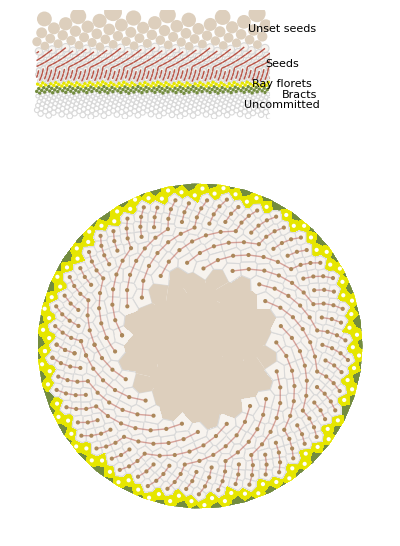

```mathematica
makescpConeTransformation :=Module[{},
runCone= getRunByTag["radius-34bis-crecrease"]["Run"];
stemParameters = runCone["Arena"]["rFunctionList"] ;
stemParameters = KeyMap[<|1->"cone",2->"bract",3->"ray",4->"seed",5->"inner"|>[#]&,stemParameters];
diskRun = DiskStacking`pruneRun[runCone,{stemParameters["bract"]["zStart"],stemParameters["inner"]["zEnd"]}];
diskShow :=makeDiskGraphics[diskRun];
cylinderRun = DiskStacking`pruneRun[runCone,{stemParameters["cone"]["zStart"],stemParameters["inner"]["zEnd"]}];
cylinderShow = makeCylinderGraphics[cylinderRun];
 GraphicsColumn[{cylinderShow,diskShow},Frame->False]
];
tlkConeTransformation=makescpConeTransformation
jExport[tlkConeTransformation]
```

### Stem map

```mathematica
polygonTransform[p_Polygon,transform_]:= Module[{listTransform},
listTransform[x_] := Map[transform,x];
Polygon[listTransform /@ (List@@p)]
];
```

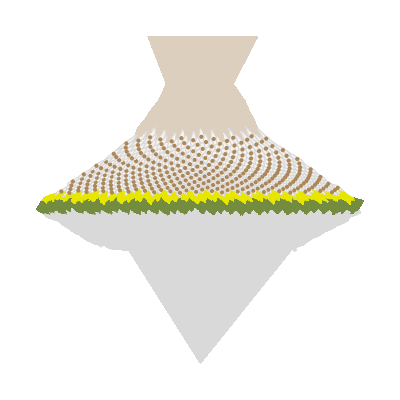

```mathematica
makeStemGraphics[run_] := Module[{},
rzData = Transpose[{Values@runDisksHeight[run,bareOnly=True],Values@runDisksRadius[run,bareOnly=True]}];
rzFunction = Interpolation[rzData];
Off[InterpolatingFunction::dmval];

zFlatten[z_] := Module[{},
If[z<stemParameters["ray"]["rEnd"],Return[z]];
stemParameters["ray"]["rEnd"]+ (z - stemParameters["ray"]["rEnd"])/10
];

rzTransform  = Function[{xz},Module[{x,z,rScale},
{x,z}=xz;
rScale = rzFunction[z];
x = x/rScale;
{x,zFlatten[z]}
]
];
namedType = nodeType /@  runDisksDivergenceHeight[run,True];

cylinderNodes =  runDisksDivergenceHeight[run,True];
namedNodes = rzTransform /@ runDisksDivergenceHeight[run,True];
colouredNodes= Association@Map[#->{cylinderNodeColour[namedType[#]],PointSize[Small],Point[namedNodes[#]]}&,Keys[namedNodes]];

cylinderPolygons = namedPointsPeriodicToVoronoiPolygons[cylinderNodes];
stemPolygons = Map[polygonTransform[#,rzTransform]&,cylinderPolygons];
colouredPolygons =Map[{polygonColour[namedType[#]],EdgeForm[polygonBoundaryColour[namedType[#]]],stemPolygons[#]}&,
Keys@stemPolygons];
 
(*namedDisks = runDisks[run];
colouredDisks= Association@Map[#->{
FaceForm[cylinderDiskColour[namedType[#]]]
,EdgeForm[cylinderDiskBoundaryColour[namedType[#]]]
,namedDisks[#]}&,Keys[namedDisks]];

seedRun=DiskStacking`pruneRun[run,{stemParameters["seed"]["zStart"],stemParameters["seed"]["zEnd"]}];
seedParastichyLeft = Select[graphToContactLines[seedRun,leftRightColours],First[#]==leftRightColours[[1]]&];
*)
Graphics[{colouredPolygons,Values@colouredNodes}(*,PlotRange ->{{-70,70},{0,1}}*), AspectRatio->1,Axes->False]
];
makeStemGraphics[cylinderRun]
```

```mathematica
makeStemGraphics3D[run_] := Module[{},
rzData = Transpose[{Values@runDisksHeight[run,bareOnly=True],Values@runDisksRadius[run,bareOnly=True]}];
minimumRadius = Min[Last/@rzData];
rzData = Map[{#[[1]],#[[2]]/minimumRadius}&,rzData];

rzFunction = Interpolation[rzData];
Off[InterpolatingFunction::dmval];

zFlatten[z_] := Module[{},
If[z<stemParameters["ray"]["zEnd"],Return[z]];
stemParameters["ray"]["zEnd"]+ (z - stemParameters["ray"]["zEnd"])/10
];


rz3Transform =  Function[{xz},Module[{x,z,stemRadius,theta},
{x,z}= xz;
stemRadius = 1/rzFunction[z];
theta = x * 2 π;
{stemRadius * Cos[theta],stemRadius*Sin[theta],zFlatten[z]}
]
];

namedType = nodeType /@  runDisksDivergenceHeight[run,True];

cylinderNodes =  runDisksDivergenceHeight[run,True];
namedNodes = rz3Transform /@ runDisksDivergenceHeight[run,True];
colouredNodes3D= Association@Map[#->{cylinderNodeColour[namedType[#]],PointSize[Small],Point[namedNodes[#]]}&,Keys[namedNodes]];

cylinderPolygons = namedPointsPeriodicToVoronoiPolygons[cylinderNodes];
stemPolygons = Map[polygonTransform[#,rz3Transform]&,cylinderPolygons];
colouredPolygons3D =Map[{polygonColour3D[namedType[#]],EdgeForm[polygonBoundaryColour[namedType[#]]],stemPolygons[#]}&,
Keys@stemPolygons];
 

Graphics3D[{colouredPolygons3D,Values@colouredNodes3D},PlotRange->{0.13,0.26},BoxRatios->{1,1,1.5},ViewPoint->Front,Boxed->False]
];
makeStemGraphics3D[cylinderRun]
```

-Graphics3D-